when doing a lot of maths, we need someone way to be absolutely sure that no mistake has been made . One way is just to reduce things several times, and through different routes . I think you must have done that, as I' ve never found any mistakes . I personally tend to deduce things on paper, then check them in Mathematica. I’ll show you how I do this below.

```mathematica
Below I check equation (29) which relates the potentials to the stress
```

```mathematica
ClearAll[subBessel];

(*the stress from the strain*)
σfun[ϵ_]:= λ Tr[ϵ] IdentityMatrix[3] + 2 μ ϵ

(*the stain from the displacement vector*)
ϵfun[u_] :=Module[{},
 ϵ1 = Grad[u,{r,θ,z},"Cylindrical"];
Return[ϵ1/2+ϵ1ᵀ/2]
]

(*the displacement vector from the potentials*)
ufun[ϕ_,ψ_] := Grad[ϕ,{r,θ,z},"Cylindrical"]+ 
Curl[{0,0,ψ},{r,θ,z},"Cylindrical"]

(*Some quick checks*)

(* Checked: this is the same as the displacement equation in the report*)
ufun[ϕ[r,θ],ψ[r,θ]]//MatrixForm

(* Checked: this is the same as the strain equation in the report*)
ϵfun[{ur[r,θ],uθ[r,θ],0}]//MatrixForm;

(* Checked: this is the same as the first equation in the report that gives the stress in terms of the displacement*)
σfun[ϵfun[{ur[r,θ],uθ[r,θ],0}]][[1;;2,1]]//Simplify

σfun[ϵfun[ufun[ϕ[r,θ],ψ[r,θ]]]][[1;;2,1]]//Simplify;
```

((ψ^(0,1)[r,θ])/r+ϕ^(1,0)[r,θ]
(ϕ^(0,1)[r,θ])/r-ψ^(1,0)[r,θ]
0)

{(λ ur[r,θ]+λ uθ^(0,1)[r,θ]+r (λ+2 μ) ur^(1,0)[r,θ])/r,(μ (-uθ[r,θ]+ur^(0,1)[r,θ]+r uθ^(1,0)[r,θ]))/r}

```mathematica
(*The equation relating the potentials to the stress in the report was*)
(*Σ[ϕ_,ψ_]:= ρ { (2 cS^2 kP^2 -  ω^2  )ϕ +  2 cS^2 D[ϕ,{r,2}] +  2 cS^2 D[1/r D[ψ,θ],r],2 cS^2 D[1/r D[ϕ,θ],r] - ω^2 ψ -2 cS^2 D[ψ,{r,2}]}*)
(*Note the simplification ω^2-> cS^2 kS^2*)
Σ[ϕ_,ψ_]:= ρ cS^2{ (2 kP^2 -   kS^2)ϕ +  2  D[ϕ,{r,2}] +  2 D[1/r D[ψ,θ],r],2 D[1/r D[ϕ,θ],r] -  kS^2 ψ -2D[ψ,{r,2}]}

(*Let's check if they are the same*)
$Assumptions={r2>0,r1>0,r>0,0<θ<2π};

subBessel[m_] = {BesselJ[m,kr_] :> kr/(2 m) (BesselJ[m-1,kr] + BesselJ[m+1,kr] ) };

n=-4;
Nϕ= BesselJ[n, r kP] ⅇ^(ⅈ n θ);

n=1;
Nψ= BesselJ[n, r kS] ⅇ^(ⅈ n θ);
σ2 =(σfun@ϵfun@ufun[Nϕ ,Nψ])[[1]][[1;;2]];
σ2-Σ[Nϕ,Nψ]//.{μ -> ρ cS^2,λ -> ρ cP^2-2 μ}/.{cS -> ω/kS,cP -> ω/kP} //FullSimplify
```

{0,0}

### Extract the stress and displacement on some boundary for one mode

```mathematica
ClearAll[n]
submodes = {ϕ -> a[n]BesselJ[n,kP r] ⅇ^(ⅈ n θ) + b[n]HankelH1[n,kP r] ⅇ^(ⅈ n θ),ψ -> c[n]BesselJ[n,kS r] ⅇ^(ⅈ n θ) + d[n]HankelH1[n,kS r] ⅇ^(ⅈ n θ)};
 Σmodes= Σ[ϕ/.submodes,ψ/.submodes];
umodes= ufun[ϕ/.submodes,ψ/.submodes][[1;;2]];

coes = {a[n],b[n],c[n],d[n]};
Σn =Coefficient[Σmodes,#]&/@coes;
Σn = Σnᵀ //Simplify;

un =Coefficient[umodes,#]&/@coes;
un = unᵀ //Simplify;

(*A quick check*)
Σn.coes == Σmodes//Simplify
un.coes == umodes//Simplify

(*Pressure potential modes*)
Σn[[All,1]] //MatrixForm//Simplify
un[[All,1]]  //MatrixForm//Simplify

(*Shear potential modes*)
Σn[[All,3]] //MatrixForm//Simplify
un[[All,3]]  //MatrixForm//Simplify
```

True

True

(-(cS^2 ⅇ^(ⅈ n θ) ρ (2 kP r BesselJ[-1+n,kP r]+(-2 n-2 n^2+kS^2 r^2) BesselJ[n,kP r]))/r^2
(ⅈ cS^2 ⅇ^(ⅈ n θ) n ρ (kP r BesselJ[-1+n,kP r]-2 BesselJ[n,kP r]-kP r BesselJ[1+n,kP r]))/r^2)

(1/2 ⅇ^(ⅈ n θ) kP (BesselJ[-1+n,kP r]-BesselJ[1+n,kP r])
(ⅈ ⅇ^(ⅈ n θ) n BesselJ[n,kP r])/r)

((ⅈ cS^2 ⅇ^(ⅈ n θ) n ρ (kS r BesselJ[-1+n,kS r]-2 BesselJ[n,kS r]-kS r BesselJ[1+n,kS r]))/r^2
(cS^2 ⅇ^(ⅈ n θ) ρ (2 kS r BesselJ[-1+n,kS r]+(-2 n-2 n^2+kS^2 r^2) BesselJ[n,kS r]))/r^2)

((ⅈ ⅇ^(ⅈ n θ) n BesselJ[n,kS r])/r
-1/2 ⅇ^(ⅈ n θ) kS (BesselJ[-1+n,kS r]-BesselJ[1+n,kS r]))

```mathematica
Σn2 = Σn/ⅇ^(ⅈ n θ) /.{ ρ -> (r^2 ρS)/cS^2, BesselJ[n_,a_]:> Subscript[J, n][a], HankelH1[n_,a_]:> Subscript[H, n][a]} //Simplify;

un2 = un/ⅇ^(ⅈ n θ) /.{  BesselJ[n_,a_]:> Subscript[J, n][a], HankelH1[n_,a_]:> Subscript[H, n][a]} //Simplify;
```

```mathematica
(*Extract only the 1st and 3rd column of the stress mode*)
Vs =Transpose[Σn2][[{1,3}]];

(*A quick check that swapping J for H turns the 1st column into 2nd, and the 3rd column into the 4th*)
Transpose[{Vs[[1]],Vs[[1]]/.J->H,Vs[[2]],Vs[[2]]/.J->H}] == Σn2 //Simplify
Vs[[1]]/.{Subscript[J, n_][a_] :> J[n,a]}
Vs[[2]]/.{Subscript[J, n_][a_] :> J[n,a]}

(*Extract only the 1st and 3rd column of the displacement mode*)
Vs =Transpose[un2][[{1,3}]];

(*A quick check that swapping J for H turns the 1st column into 2nd, and the 3rd column into the 4th*)
Transpose[{Vs[[1]],Vs[[1]]/.J->H,Vs[[2]],Vs[[2]]/.J->H}] == un2 //Simplify
Vs[[1]]/.{Subscript[J, n_][a_] :> J[n,a]}
Vs[[2]]/.{Subscript[J, n_][a_] :> J[n,a]}
```

True

{-ρS (2 kP r J[-1+n,kP r]+(-2 n-2 n^2+kS^2 r^2) J[n,kP r]),ⅈ n ρS (kP r J[-1+n,kP r]-2 J[n,kP r]-kP r J[1+n,kP r])}

{ⅈ n ρS (kS r J[-1+n,kS r]-2 J[n,kS r]-kS r J[1+n,kS r]),ρS (2 kS r J[-1+n,kS r]+(-2 n-2 n^2+kS^2 r^2) J[n,kS r])}

True

{1/2 kP (J[-1+n,kP r]-J[1+n,kP r]),(ⅈ n J[n,kP r])/r}

{(ⅈ n J[n,kS r])/r,-1/2 kS (J[-1+n,kS r]-J[1+n,kS r])}

```mathematica
Formulate the matrix M and do some numerical checks;

(* The simplest direct problem: specify the forcing everywhere on an inner and outer radius*)
(* This allows for a Fourier type solution shown below*)

eqs =(Σmodes/.r-> r1)~Join~(Σmodes/.r->r2);
coes = {a[n],b[n],c[n],d[n]};
M =Coefficient[eqs/ⅇ^(ⅈ n θ) ,#]&/@coes;
M = Mᵀ //Simplify;
(*A quick check*)
M.coes == eqs/ⅇ^(ⅈ n θ)  //Simplify

M
```

True

```mathematica
(*Numerical check of stability*)
(*Even with condition number 10^8 we can still get solutions with accuracy around 10^-8, this is because Float64, the most common floating number has a precision of 10^-16*)
subN = {cS -> 1.0, cP -> 2.0,r1 -> 0.5,r2 -> 1.0,ρ-> 1.0};
NM = M/.{θ->0 ,kP -> ω/cP,kS -> ω/cS}//.subN;

n0 = 6;ω0 = 5.1;
Nb = RandomReal[4,4];
Ncoes = LinearSolve[NM/.{n->n0,ω ->ω0 },Nb];
Norm[NM.Ncoes - Nb/.{n->n0,ω ->ω0 }] / Norm[Nb]
```

3.04574×10^-15

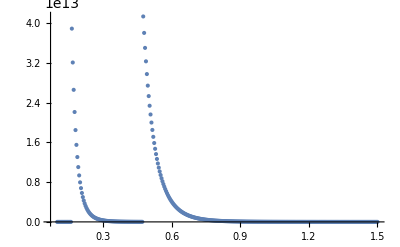

```mathematica
(*A bit of a strange pattern, am not sure why*)
CondNum[A_]:=  (
sv = SingularValueList[A/.{n->n0,ω ->ω0 }];
sv[[1]]/Last@sv
)
ωs=Range[0.1,1.5,0.004];
CondNum[NM/.{n->4,ω -># }]&/@ωs;
ListPlot[Transpose[{ωs,%}],PlotRange->All]

(*I'm guessing the peaks are the resonant frequencies?*)
```

```mathematica
Question: we solved the forward problem by prescribing the stress on both surfaces. Could we formulate an equivalent forward problem by prescribing the stress and displacement only on the surface r = r2? This should be the same method you as developed Jess
```

```mathematica
eq1 = Σ[ϕ/.submodes,ψ/.submodes]/.r->r2;
 eq2=ufun[ϕ/.submodes,ψ/.submodes][[1;;2]]/.r->r2;
eqs = eq1~Join~eq2//Simplify;

coes = {a[n],b[n],c[n],d[n]};
M2 =Coefficient[eqs,#]&/@coes;
M2 = M2ᵀ //Simplify;
(*A quick check*)
M2.coes == eqs//Simplify

(*Numerical check of stability, seems very stable*)
subN = {cS -> 1.0, cP -> 2.0,r1 -> 0.5,r2 -> 1.0,ρ-> 1.0};
NM = M2/.{θ->0 ,kP -> ω/cP,kS -> ω/cS}//.subN;

n0 = 8;ω0 = 5.1;
Nb = RandomReal[4,4];
Ncoes = LinearSolve[NM/.{n->n0,ω ->ω0 },Nb];
Norm[NM.Ncoes - Nb/.{n->n0,ω ->ω0 }] / Norm[Nb]
```

True

1.94598×10^-15

```mathematica
M2/ⅇ^(ⅈ n θ)//Simplify//MatrixForm
```

(-(cS^2 ρ (2 kP r2 BesselJ[-1+n,kP r2]+(-2 n-2 n^2+kS^2 r2^2) BesselJ[n,kP r2]))/r2^2 | -(cS^2 ρ (2 kP r2 HankelH1[-1+n,kP r2]+(-2 n-2 n^2+kS^2 r2^2) HankelH1[n,kP r2]))/r2^2 | (ⅈ cS^2 n ρ (kS r2 BesselJ[-1+n,kS r2]-2 BesselJ[n,kS r2]-kS r2 BesselJ[1+n,kS r2]))/r2^2 | (ⅈ cS^2 n ρ (kS r2 HankelH1[-1+n,kS r2]-2 HankelH1[n,kS r2]-kS r2 HankelH1[1+n,kS r2]))/r2^2
(ⅈ cS^2 n ρ (kP r2 BesselJ[-1+n,kP r2]-2 BesselJ[n,kP r2]-kP r2 BesselJ[1+n,kP r2]))/r2^2 | (ⅈ cS^2 n ρ (kP r2 HankelH1[-1+n,kP r2]-2 HankelH1[n,kP r2]-kP r2 HankelH1[1+n,kP r2]))/r2^2 | (cS^2 ρ (2 kS r2 BesselJ[-1+n,kS r2]+(-2 n-2 n^2+kS^2 r2^2) BesselJ[n,kS r2]))/r2^2 | (cS^2 ρ (2 kS r2 HankelH1[-1+n,kS r2]+(-2 n-2 n^2+kS^2 r2^2) HankelH1[n,kS r2]))/r2^2
1/2 kP (BesselJ[-1+n,kP r2]-BesselJ[1+n,kP r2]) | 1/2 kP (HankelH1[-1+n,kP r2]-HankelH1[1+n,kP r2]) | (ⅈ n BesselJ[n,kS r2])/r2 | (ⅈ n HankelH1[n,kS r2])/r2
(ⅈ n BesselJ[n,kP r2])/r2 | (ⅈ n HankelH1[n,kP r2])/r2 | 1/2 kS (-BesselJ[-1+n,kS r2]+BesselJ[1+n,kS r2]) | -1/2 kS (HankelH1[-1+n,kS r2]-HankelH1[1+n,kS r2]))

```mathematica
2nd Question: what we want is to predict Subscript[σ, r2] the stressed at r == r2  The space of possible stress Subscript[σ, r2] is smaller than the space of possible waves in the cylinder (given by the coefficients); So solving for the coefficients maybe over kill. Can we instead formulate a system to solve just in terms of Subscript[σ, r2]? See image of notes added in this folder.
```

```mathematica
Formulate the inverse problem: measure displacement, predict the stress
```

```mathematica
ClearAll[U]
(*Find the map from the coefficients to the displacement*)
term= ufun[ϕ/.submodes,ψ/.submodes][[1;;2]];
U[r_] = Coefficient[term,#]&/@coes;
U[r] = U[r]ᵀ //Simplify;
U[r].coes == term //Simplify


U[r]//MatrixForm

Σ[ϕ[r,θ],ψ[r,θ]];
```

True

(1/2 ⅇ^(ⅈ n θ) kP (BesselJ[-1+n,kP r]-BesselJ[1+n,kP r]) | 1/2 ⅇ^(ⅈ n θ) kP (HankelH1[-1+n,kP r]-HankelH1[1+n,kP r]) | (ⅈ ⅇ^(ⅈ n θ) n BesselJ[n,kS r])/r | (ⅈ ⅇ^(ⅈ n θ) n HankelH1[n,kS r])/r
(ⅈ ⅇ^(ⅈ n θ) n BesselJ[n,kP r])/r | (ⅈ ⅇ^(ⅈ n θ) n HankelH1[n,kP r])/r | -1/2 ⅇ^(ⅈ n θ) kS (BesselJ[-1+n,kS r]-BesselJ[1+n,kS r]) | -1/2 ⅇ^(ⅈ n θ) kS (HankelH1[-1+n,kS r]-HankelH1[1+n,kS r]))